## Observer-based feedback for undamped, unstable oscillator; simulate combined system Problem 4.9

```mathematica
Clear["Global`*"]                                              (* clear everything *)
```

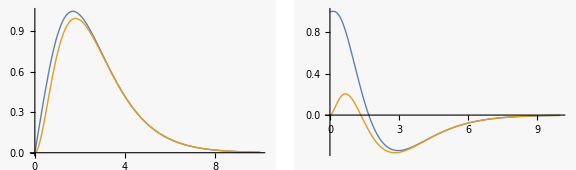

```mathematica
G0=1/(s^2-1); G0tf=TransferFunctionModel[G0,s];G0ss = StateSpaceModel[G0tf,SystemsModelLabels->{{"y"},{"u"},{"x","xdot"}}]; 
K = StateFeedbackGains[G0ss,{-1,-1}]   (* Feedback gains *);
L=EstimatorGains[G0ss,{-2,-2}]         (* Observer gains; note sign convention! *);
{A,b,c,d}=Normal[G0ss]  (* get A, b, c matrices *);
A1= A-b.K; 
G1ss = StateSpaceModel[{A1,b,c,d}];
A2 = A-b.K-L.c; Ac = ArrayFlatten[({{A, -b.K}, {L.c, A2}})]; (* for "big" system *)
kr = -1/(c.Inverse[A1].b);             (* feedforward gain for reference command *)
Br= ArrayFlatten[({{b.kr}, {b.kr}})];  (* input coupling for reference [not used here] *)
Bd =  ArrayFlatten[({{b}, {0}, {0}})];  (* assume disturbance couples through input *)
Btot = ArrayFlatten[ ({{Br, Bd}})];   (* assemble the "big" input-coupling matrix *)
G1ss = StateSpaceModel[{Ac,Btot}]; (* the full system, w/o output coupling *)
u=({{0}, {DiracDelta[t]}})  (* no reference; disturb state *);
(* u=({{UnitStep[t]}, {DiracDelta[t-5]}})  (* alternate input with ref. step & disturbance *) *)
{θ,θd,θh,θhd} = StateResponse[G1ss,u,t]//Simplify;
tmax=10; 
p1=Plot[{θ,θh},{t,0,tmax},PlotRange->Full,PlotStyle ->{Thick}];
p2=Plot[{θd,θhd},{t,0,tmax},PlotRange->Full,PlotStyle ->{Thick},Exclusions->None];
GraphicsRow[{p1,p2},ImageSize->Large]
```

```mathematica
TraditionalForm/@{θ,θd,θh,θhd}
```

{ⅇ^(-2 t) (6 t+ⅇ^t (9 t-14)+14) t,-ⅇ^(-2 t) (12 t+ⅇ^t (9 t-23)+22) t,ⅇ^(-2 t) (5 t+ⅇ^t (9 t-14)+14) t,-ⅇ^(-2 t) (14 t+ⅇ^t (9 t-23)+23) t}

```mathematica
{G0ss,G1ss}
```

{010101100yuxxdotStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2yuxxdotIdentityAutomatic112111213132TrueTrueFalseAutomaticyuxxdotAutomatic,01000010-2-21140-410050-6-210StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2-441FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
MatrixForm /@{Ac,K,L,A}
```

{(0 | 1 | 0 | 0
1 | 0 | -2 | -2
4 | 0 | -4 | 1
5 | 0 | -6 | -2),(2 | 2),(4
5),(0 | 1
1 | 0)}

```mathematica
Kob = K.Inverse[s({{1, 0}, {0, 1}})-A2].L // Simplify;
KobTF=TransferFunctionModel[Kob,s]
```

(18 (1+s))/(14+6 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1118141FalseFalseFalseAutomaticNoneAutomatic

## Redo using Mathematica system commands

```mathematica
estreg=StateSpaceModel[EstimatorRegulator[G0ss,{L,K}],SystemsModelLabels->{{"y"},{"u"},{"x̂","x̂dot"}}]
```

-414-6-25220yux̂x̂dotStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2yux̂x̂dotIdentityAutomatic112111213132TrueTrueFalseAutomaticyux̂x̂dotAutomatic

```mathematica
closedLoop=StateSpaceModel[SystemsModelFeedbackConnect[G0ss,estreg],SystemsModelLabels->{{"u"},{"y"},{"x","xdot","x̂","x̂dot"}}]
```

0100010-2-2140-41050-6-2010000uyxxdotx̂x̂dotStateSpaceModelTrueTrueTrueFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4uyxxdotx̂x̂dotIdentityAutomatic1141112131323334TrueTrueFalseAutomaticuyxxdotx̂x̂dotAutomatic

```mathematica
{xs,xds,xe,xde}=StateResponse[{closedLoop,{0,1,0,0}},0,t];
p1a=Plot[{xs,xe},{t,0,tmax},PlotRange->All];
p2a=Plot[{xds,xde},{t,0,tmax},PlotRange->All];
GraphicsRow[{p1a,p2a},ImageSize->Large]
```

-Graphics-